# 1-D universal estimator using DNN

Given the pdf of some distribution and a sample containing m observations drawn from dist using pdf with true parameter θ, The UniversalEstimator(pdf, sample, θ) returns  a tuple (Overscript[θ, ^], e, CRB) where Overscript[θ, ^] is the predicted parameter, e is the abs-error | θ - Overscript[θ, ^] | and CRB is the Cramer-Rao-Bound (θ, m) of the distribution with θ.

### Fisher Information

```mathematica
(*Module is to state that {x,y......} inside the [] is local symbol]*)
```

Fisher information for a distribution with a single parameter θ

```mathematica
FisherInformation[dist_]:=Module[{f},
(*let f be the PDF of dist with parameter θ evaluated at x*)
f = PDF[dist[θ],x];
Expectation[D[Log[f], {θ}]^2,x\[Distributed]dist[θ]]  (*the return of this function*)
]
```

### Cramer-Rao bound

Cramer-Rao bound for a single parameter d and m observations

```mathematica
CRB[dist_, d_, m_]:=(
fi=FisherInformation[dist];
FI[θ_]:=Evaluate[fi];
(1/FI[d])/m  (*the return of this function*)
)
```

#### Examples

#### Poisson distribution

```mathematica
FisherInformation@PoissonDistribution
```

1/θ

```mathematica
CRB[PoissonDistribution, 3, 2048]
```

3/2048

#### Geometric distribution

```mathematica
FisherInformation@GeometricDistribution
```

-1/((-1+θ) θ^2)

```mathematica
CRB[GeometricDistribution, 0.5, 2048]
```

0.0000610352

#### Normal distribution

```mathematica
NormalDistribution1D[σ_]:=NormalDistribution[0,σ];
```

```mathematica
FisherInformation@NormalDistribution1D
```

2/θ^2

```mathematica
CRB[NormalDistribution1D, 3, 2048]
```

9/4096

## Generating data (without duplicating θ and logging the histogram)

Generates synthetic data for DNN :

Arguments:
	n: number of samples drawn for a given θ 
	M: number of different θ generated in the range [min_θ, max_θ]
	S: number of samples per θ 
	f: the distribution function for generating samples. f(θ, N) returns N observations using parameter θ
	range: range of the dist parameter θ
	bins: number of bins in the histograms generated from samples: max[samples] or max[samples]+1 (with zero padding)
Return:
	a table of associations(one row per sample): histogram->θ

```mathematica
GenerateData[M_, n_, f_, range_, bins_:-1]:=
	Module[{params, samples, nbins, MAXBINS},
		params=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
		(*generate M different random initparameters in the range [min_θ,max_θ]*) 
		samples=Table[f[params[[i]],n],{i,1,M}];
		(*generate M distributions, each distribution has n number/data*, now we have M*n data*)
		MAXBINS=5000;
		nbins=If[bins>0,bins,Min[MAXBINS, Ceiling[Max[samples]]+1](*Ceiling[Max[samples]]+2] if using zero padding*)];
		h[x_]:=HistogramList[x,{0,nbins,1}][[2]]; (*without using log10(x+1)*)
		Table[h@samples[[i]]->params[[i]], {i,1,M}]  
	
	]
```

## Example of generated data

```mathematica
(*f[å_,N_]:=RandomVariate[WaringYuleDistribution[å],N];
Print[GenerateData[5,10,f,{2,3}]//TableForm];*)
```

{6,3,0,1}→2.67938
{6,0,4,0}→2.21798
{7,1,1,1}→2.25193
{7,2,1,0}→2.76568
{6,1,1,2}→2.16986

## DNN

Generate a DNN for predicting the parameter θ from the distribution histogram
The input size is the number of bins in the input histogram, the output is a scalar predicting the parameter used to generate the input sample.

```mathematica
CreateNet[bins_]:=( 
NetChain[{
LinearLayer[bins],  
BatchNormalizationLayer[],  (*batch normaliztiozion*)
ElementwiseLayer[Ramp], (*Ramp is the relu*)

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[1]
},
"Input"->bins, 
"Output" -> "Scalar"]
)
```

## 1-D universal estimator using DNN

Given a distribution  dist(x|θ) and the range for the parameter θ,  
UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_]:=Module[{g, M, n, trainSet, bins, valSet ,net, trained, model, h},
(*define a sample generator*)
g[θ_,n_] := RandomVariate[dist[θ],n];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
M = 10000; 
n = 1024;   (*number of observations in each sample*)
trainSet=GenerateData[M,n, g, range];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[M/2,n, g, range, bins];

(*Create and train the NN*)
net = NetInitialize@CreateNet[bins];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>, (*using loss criterion to prevent overfitting*)
Method->"ADAM" ,
BatchSize->1024
 
];

Print[trained];  (*print the training result*)

model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=HistogramList[x,{0,bins,1}][[2]];

(*return an Estimator which is a fucntion map sample to a parameter*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiment of universal estimator with DNN

n : number of samples drawn for a given θ 
M : number of different θ generated in the range [min_θ, max_θ]
S : number of samples per θ

```mathematica
RunExperiment[dist_, range_]:= Module[{estimator, g, adjuster, params, n, samples, Θ, Θhat, e, TestSet, M, initΘ, expansion,S, crb,Var, Average, Averagelist},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range];
(*define the size of the test set*)
M = 10;
S = 100；
n = 1024;

initΘ=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
(*generate M different random initΘ in the range [min_θ,max_θ]*)
expansion[j_]:=Table[initΘ[[j]],S]; 
(*define an expansion function for duplicating the initΘ*)
Θ=Flatten[Table[expansion[w],{w,1,M}]];
(*increase the number of each different parameters to S, now we have M*S Θ *)		
g[θ_,a_] := RandomVariate[dist[θ],a];
(*create M*S test samples*)
samples = Table[g[Θ[[i]], n], {i,1,M*S,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,M*S,1 }];
(*Compute Cramer-Rao bound at Subscript[θ, i]*)
crb = Table[CRB[dist, initΘ[[i]], n], {i,1,Length[initΘ]}];
(*evaluate prediction errors*)
e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,M*S,1 }];
(*Compute the varience of each Subscript[θ, i]*)
Averagelist= Partition[Θhat,S];
Average = Table[Mean[Averagelist[[i]]], {i,1,Length[initΘ]}];
Var = Table[Mean[(Averagelist[[i]]-Average[[i]])^2], {i,1,Length[initΘ]}];

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
Print["Difference between the true θ and the Mean for each θ: ", Abs[Average-initΘ]];
Print["Variance for each θ:",Var];
Print["crb for each θ:",crb];
Print["ratio of variance and crb for each θ:",Var/crb];
Print["RMSE:",RootMeanSquare[e]];


(*return true parameters and predicted errors*)
{Θ, e}
]
```

## Run the experiment for different distributions

### Poisson distribution

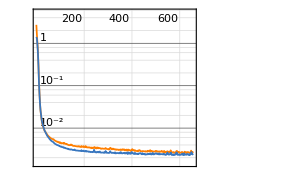
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:6560  rounds:656  time:42s  examples/s:161954
data | ,,  training examples:10000  validation examples:5000  processed examples:6717440  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:2.58×10^-3
validation | ,,  loss:2.31×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.71858,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.72412,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.93154,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.08905,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.73989,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.2796,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.95066,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.98558,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.34482,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622,2.36622}

θ̂: {2.67523,2.62129,2.66567,2.72164,2.79265,2.77666,2.6975,2.75135,2.7474,2.69907,2.69611,2.71045,2.62688,2.69379,2.75635,2.69193,2.76024,2.63776,2.73381,2.79906,2.81264,2.62682,2.63878,2.77016,2.69129,2.79413,2.77294,2.71328,2.68239,2.67487,2.80768,2.78076,2.64786,2.6294,2.77415,2.72119,2.70871,2.80011,2.69419,2.64109,2.73447,2.69242,2.73344,2.66764,2.71841,2.71497,2.78399,2.60541,2.69004,2.76854,2.71959,2.82288,2.67233,2.68417,2.764,2.69985,2.69164,2.73135,2.72995,2.75637,2.66018,2.67209,2.65498,2.73223,2.79325,2.83579,2.72845,2.75748,2.74939,2.76527,2.72651,2.63251,2.80897,2.83206,2.76444,2.71804,2.69777,2.73073,2.57947,2.66314,2.66975,2.69483,2.71484,2.60068,2.79197,2.63131,2.75422,2.69579,2.71439,2.77225,2.82342,2.78911,2.73256,2.66278,2.7383,2.63844,2.82346,2.69949,2.69936,2.79713,2.76967,2.75171,2.65865,2.75356,2.75799,2.67813,2.73609,2.7301,2.80236,2.66984,2.77614,2.65155,2.72336,2.70624,2.67812,2.68218,2.69469,2.74192,2.73152,2.72437,2.74913,2.67466,2.71613,2.74025,2.6283,2.75992,2.78231,2.72363,2.69844,2.75276,2.70487,2.75351,2.70626,2.69719,2.7235,2.80386,2.75403,2.70978,2.73831,2.71214,2.75634,2.68987,2.71473,2.69964,2.72533,2.85115,2.72333,2.78281,2.6389,2.74523,2.62087,2.80368,2.76989,2.63192,2.72326,2.77571,2.80482,2.74356,2.77364,2.75514,2.83019,2.65872,2.71799,2.66848,2.73949,2.7089,2.63957,2.69954,2.69758,2.65712,2.74868,2.67026,2.73852,2.73364,2.67243,2.68835,2.71033,2.74923,2.64821,2.72536,2.71655,2.69605,2.68199,2.79634,2.6522,2.56471,2.66477,2.66562,2.80259,2.69648,2.79101,2.67692,2.67885,2.68667,2.64013,2.72724,2.6566,2.82759,2.78906,2.75896,2.90952,2.94333,2.89896,2.95607,2.92567,2.91501,2.92755,2.91744,2.93611,2.86091,2.87214,2.86615,2.88956,2.9198,2.90604,2.88749,2.92216,2.84501,2.87939,2.95461,2.93265,2.93593,2.91405,2.8954,2.89443,2.84563,2.9397,2.93252,2.9215,2.95173,2.90268,2.9137,2.94629,2.92489,2.89634,2.94712,2.96102,2.95129,2.93744,2.9195,2.89501,2.92631,2.89664,2.90247,2.93498,2.96267,2.93048,2.9099,2.92688,2.93806,2.94886,2.95783,2.89705,2.9184,2.93056,2.92013,2.89392,2.87732,2.96588,2.92182,2.86845,2.95561,2.91105,2.9261,2.92111,2.9404,2.86817,2.94765,2.9194,2.89064,2.91035,2.9426,2.91808,2.90085,2.91668,2.93474,2.81987,2.92748,2.94246,2.9383,2.95427,2.9491,2.91118,2.88832,2.95066,2.902,2.93051,2.87038,2.91563,2.88294,2.93741,2.94468,2.93931,2.89414,2.92923,2.89512,2.95096,2.94715,2.98689,2.92072,2.17823,2.10636,2.05106,2.06494,2.08885,2.07945,2.06778,2.08998,2.106,2.0555,2.08974,2.06437,2.07691,2.11776,2.10675,2.1146,2.07681,2.11625,2.08411,2.09134,2.06535,2.04799,2.1172,2.12175,2.15312,2.11556,2.06819,2.09626,2.08236,2.09944,2.15571,2.05141,2.09872,2.12725,2.05252,2.07773,2.12664,2.10259,2.05198,2.07984,2.10507,2.04798,2.04986,2.0852,2.11942,2.07672,2.1746,2.06441,2.05505,2.03928,2.18109,2.14639,2.11538,2.12879,2.12365,2.04819,2.06564,2.09187,2.11358,2.06981,2.13052,2.07024,2.03187,2.05311,2.02534,2.03315,2.03916,2.0452,2.04863,2.07185,2.08061,2.0609,2.09745,2.14708,2.0681,2.05304,2.15,2.08727,2.04653,2.09348,2.05578,2.17963,2.06147,2.12992,2.21569,2.13674,2.15638,2.08987,2.03874,2.03985,2.08788,2.04182,2.0775,2.06365,2.05821,2.11741,2.05377,2.13083,2.06164,2.06031,2.69616,2.65816,2.82207,2.72843,2.68392,2.81717,2.75115,2.83645,2.78144,2.58893,2.68163,2.71777,2.79671,2.6451,2.80197,2.71226,2.82608,2.67174,2.76241,2.77704,2.75995,2.68428,2.76484,2.77692,2.7648,2.69586,2.75604,2.80856,2.82526,2.72241,2.77258,2.71873,2.74638,2.75351,2.74437,2.78769,2.68238,2.80664,2.72968,2.6992,2.70263,2.74452,2.65592,2.87213,2.68972,2.72544,2.78214,2.77,2.87487,2.74717,2.7169,2.73776,2.73728,2.77164,2.83172,2.70981,2.71484,2.77919,2.77987,2.71727,2.83185,2.73288,2.76324,2.79236,2.73167,2.7936,2.71082,2.69552,2.64761,2.74314,2.79997,2.71909,2.75853,2.69144,2.66601,2.75673,2.68247,2.72136,2.76208,2.66784,2.70444,2.65227,2.76367,2.73017,2.7293,2.69796,2.73528,2.77988,2.66023,2.75572,2.81202,2.76674,2.71199,2.78923,2.68297,2.85108,2.79749,2.72075,2.67991,2.80496,2.28975,2.26596,2.25585,2.26303,2.24713,2.32226,2.3062,2.27142,2.22287,2.24481,2.29541,2.30399,2.26151,2.33728,2.25319,2.30695,2.23978,2.2548,2.24716,2.21603,2.17941,2.23542,2.2327,2.2628,2.27752,2.33787,2.26954,2.34605,2.2025,2.3091,2.29628,2.31216,2.2721,2.25022,2.26915,2.24601,2.30234,2.29389,2.27017,2.25677,2.29794,2.24611,2.23755,2.23656,2.31944,2.2635,2.23456,2.32355,2.27114,2.23704,2.19086,2.30718,2.23399,2.29944,2.27756,2.28014,2.27333,2.26262,2.23106,2.22373,2.23772,2.23363,2.31097,2.26128,2.29969,2.23642,2.20515,2.33683,2.25985,2.251,2.34855,2.23735,2.24665,2.23839,2.31004,2.27664,2.28981,2.24976,2.27637,2.24516,2.31523,2.26479,2.21625,2.2312,2.20799,2.30638,2.27188,2.36689,2.22815,2.34047,2.35024,2.18815,2.33289,2.26728,2.35985,2.33147,2.28387,2.26101,2.34759,2.29931,2.90338,2.9268,2.9047,2.90996,2.95233,2.9286,2.83973,2.92962,2.95377,2.92993,2.90533,2.91728,2.95177,2.92991,2.94226,2.93599,2.94082,2.93002,2.93252,2.96355,2.85579,2.92239,2.93918,2.97586,2.94882,2.94068,2.95122,2.92563,2.95628,2.87249,2.90538,2.94824,2.94189,2.97246,2.93264,2.96188,2.91312,2.91308,2.9046,2.9392,2.93323,2.94145,2.94158,2.89229,2.9184,2.93373,2.93736,2.96553,2.93895,2.91936,2.95946,2.92425,2.90678,2.90895,2.95368,2.96048,2.82443,2.92771,2.98162,2.93699,2.93883,2.96281,2.95072,2.8967,2.98823,2.93483,2.94969,2.92133,2.91633,2.93504,2.93001,2.9731,2.85394,2.95231,2.91178,2.89533,2.94755,2.87448,2.92928,2.94599,2.95604,2.91163,2.9663,2.9158,2.87877,2.93517,2.91949,2.94066,2.95091,2.93688,2.96396,2.85013,2.9484,2.93278,2.93622,2.93747,2.94344,2.93583,2.92934,2.92745,2.94565,2.9547,2.92501,2.9505,2.94049,2.93722,2.90892,2.96813,2.97211,2.94503,2.97125,2.93716,2.97757,2.99906,2.98267,2.89381,2.91422,2.89442,2.94502,2.9522,2.91887,2.92977,2.96477,3.00402,2.92413,2.93279,2.93652,2.9472,2.92519,3.01511,2.93539,2.89958,2.95425,2.98672,2.94796,2.97106,2.96411,2.96568,2.92365,2.9129,2.92505,2.94771,2.97357,2.93919,2.94953,2.95802,2.96877,2.94246,2.96562,2.95697,2.96139,2.95098,2.97182,2.93889,2.92165,2.92983,2.95659,2.9491,2.9565,2.97516,2.91354,2.89753,2.97079,2.93358,2.92384,2.93229,2.98509,2.92431,2.9365,2.94153,2.9344,2.96219,2.9243,2.93149,2.94622,2.94835,2.94523,2.92758,2.95956,2.95047,2.92331,2.89969,2.94497,2.92711,2.95251,2.97302,2.9799,2.83597,2.93502,2.95489,2.90352,2.95823,2.96616,2.94734,2.92111,2.91667,2.95671,2.90935,2.99358,2.92003,2.34057,2.23126,2.37899,2.32684,2.3828,2.2712,2.37521,2.3122,2.31297,2.33035,2.36705,2.3702,2.41811,2.44566,2.39073,2.30062,2.29642,2.40875,2.31279,2.24582,2.29111,2.52506,2.44654,2.28272,2.48308,2.37866,2.35318,2.34201,2.2437,2.26529,2.2919,2.42244,2.36341,2.34321,2.32163,2.36509,2.35661,2.39126,2.34585,2.30541,2.32668,2.33562,2.36585,2.36149,2.28226,2.38986,2.43221,2.38105,2.27965,2.37497,2.32777,2.24138,2.37792,2.30053,2.30097,2.33541,2.29154,2.28811,2.45431,2.40088,2.37255,2.27713,2.28835,2.40127,2.45466,2.27627,2.25534,2.28599,2.32555,2.32903,2.36447,2.33053,2.34595,2.30907,2.42353,2.37337,2.35279,2.37147,2.30934,2.23997,2.27417,2.35264,2.26822,2.37417,2.28966,2.46576,2.30395,2.32421,2.40832,2.31303,2.37373,2.29515,2.36458,2.32621,2.29289,2.36964,2.30374,2.33331,2.41695,2.41739,2.33817,2.31927,2.35471,2.41796,2.45975,2.35869,2.31863,2.25787,2.3088,2.39637,2.48006,2.38516,2.40236,2.38603,2.30953,2.38215,2.51429,2.43793,2.44377,2.33706,2.3697,2.35309,2.22292,2.19858,2.3184,2.30785,2.37409,2.32341,2.30384,2.46257,2.38951,2.42206,2.35226,2.38926,2.39463,2.29893,2.39023,2.43065,2.35851,2.42235,2.36095,2.38494,2.37283,2.32133,2.32823,2.29984,2.30282,2.3685,2.46428,2.36136,2.41967,2.36854,2.32198,2.447,2.34595,2.35737,2.40284,2.40007,2.34799,2.34776,2.32832,2.40863,2.45006,2.41655,2.35302,2.36487,2.49936,2.47163,2.3082,2.41708,2.42871,2.28704,2.37115,2.33797,2.3863,2.40654,2.37759,2.40702,2.42426,2.44482,2.35544,2.30538,2.38712,2.28699,2.37151,2.42,2.41386,2.38859,2.44207,2.33022,2.50674,2.2914,2.32583,2.4446,2.48373,2.33126,2.25049,2.34468,2.32138,2.34428}

abs(θ-θ̂): {0.0433454,0.0972881,0.0529084,0.0030656,0.0740767,0.058084,0.0210719,0.0327783,0.0288263,0.0195064,0.0224638,0.00812481,0.0916972,0.0247841,0.0377698,0.0266433,0.0416675,0.0808158,0.0152331,0.0804787,0.094059,0.0917563,0.0798006,0.0515857,0.0272913,0.0755525,0.054359,0.0052924,0.03619,0.0437112,0.0891028,0.0621824,0.0707145,0.0891733,0.055572,0.00261499,0.00987004,0.0815358,0.0243897,0.0774894,0.0158911,0.026155,0.0148616,0.0509386,0.00017117,0.0036044,0.0654102,0.113168,0.0285354,0.0499606,0.001009,0.104302,0.0462422,0.0344038,0.0454197,0.0187287,0.0269375,0.0127702,0.0113735,0.0377889,0.058393,0.0464825,0.0635981,0.0136523,0.0746689,0.117216,0.0098734,0.0389066,0.0308156,0.0466943,0.00792886,0.0860648,0.0903888,0.113483,0.0458655,0.000533567,0.0208058,0.012157,0.139103,0.055438,0.0488243,0.0237508,0.00374125,0.117901,0.0733895,0.0872626,0.0356398,0.0227856,0.00419138,0.0536719,0.104843,0.0705376,0.0139866,0.0557995,0.019723,0.0801329,0.104884,0.0190854,0.0192146,0.0785566,0.0455533,0.0275913,0.0654644,0.029441,0.0338694,0.0459823,0.0119783,0.00598775,0.0782472,0.0542811,0.0520245,0.0725707,0.000753769,0.0178722,0.0459999,0.0419325,0.0294231,0.0178014,0.00740587,0.000252834,0.0250097,0.0494536,0.00798977,0.0161377,0.0958184,0.0358058,0.0581919,0.000482925,0.025679,0.0286428,0.0192493,0.0293971,0.0178608,0.0269231,0.000613102,0.0797483,0.0299112,0.0143341,0.014197,0.0119747,0.0322272,0.0342454,0.00938357,0.0244764,0.00120889,0.127033,0.000789532,0.0586935,0.0852178,0.0211183,0.103251,0.0795613,0.0457741,0.092194,0.000861057,0.0515944,0.0806991,0.0194465,0.0495206,0.0310255,0.106072,0.0653995,0.00612677,0.0556315,0.0153729,0.0152205,0.0845493,0.0245785,0.0265411,0.066995,0.0245625,0.053861,0.0144058,0.00952636,0.0516876,0.0357636,0.0137853,0.025118,0.0759066,0.00124418,0.00756443,0.0280699,0.0421218,0.0722214,0.0719174,0.15941,0.0593499,0.0584983,0.0784713,0.0276364,0.0668899,0.0471948,0.0452665,0.0374435,0.0839843,0.0031191,0.0675172,0.10347,0.0649477,0.0348474,0.0220177,0.0117915,0.0325753,0.0245264,0.00587004,0.0165259,0.0039894,0.0140974,0.0045684,0.0706298,0.0594046,0.0653941,0.0419766,0.0117413,0.0254995,0.0440513,0.00937861,0.0865256,0.0521519,0.0230673,0.00111085,0.00438577,0.0174944,0.0361411,0.0371081,0.0859129,0.00815946,0.000975907,0.0100409,0.0201929,0.0288593,0.0178401,0.0147513,0.00665206,0.0351974,0.0155781,0.0294822,0.0197476,0.00589591,0.0120417,0.0365345,0.00522918,0.0348975,0.0290729,0.00343925,0.0311287,0.00106305,0.0216429,0.00466508,0.0065158,0.0173228,0.0262864,0.0344879,0.013139,0.000977695,0.0114056,0.0376236,0.0542247,0.0343397,0.00972194,0.0630895,0.0240725,0.0204927,0.00543708,0.0104253,0.00885612,0.063368,0.0161112,0.0121419,0.0409014,0.0211908,0.0110553,0.013456,0.0306947,0.0148565,0.00320417,0.111666,0.00406092,0.0109189,0.00676328,0.0227345,0.0175598,0.0203578,0.043224,0.0191248,0.0295426,0.00102967,0.0611579,0.0159108,0.0485985,0.00587445,0.0131372,0.00777465,0.0374004,0.00231236,0.0364248,0.0194152,0.0156124,0.0553468,0.0108234,0.0891722,0.0173064,0.0379902,0.0241169,0.000207085,0.00959982,0.0212752,0.00092588,0.0169514,0.0335552,0.000683885,0.0246848,0.0121414,0.0287098,0.0176953,0.0255488,0.012242,0.0271929,0.00494303,0.00228391,0.0237016,0.0410582,0.0281476,0.032693,0.0640639,0.0265115,0.0208579,0.00720583,0.00669612,0.0103847,0.0666584,0.0376378,0.00966774,0.0381988,0.0365359,0.0113255,0.0375827,0.013538,0.0370728,0.00920929,0.016014,0.0410763,0.0391919,0.00384964,0.0303651,0.0123364,0.0855468,0.0246445,0.0340063,0.0497679,0.0920342,0.0573405,0.0263296,0.0397352,0.0346011,0.0408641,0.0234133,0.00282083,0.0245284,0.0192415,0.0414632,0.0188178,0.0571844,0.0359386,0.0637099,0.0559017,0.0498935,0.0438503,0.0404235,0.0172059,0.00844469,0.0281493,0.00839315,0.0580276,0.0209481,0.0360106,0.060952,0.00178184,0.0425204,0.00442277,0.0332776,0.090577,0.0275854,0.0408691,0.126635,0.0476874,0.0673288,0.000820499,0.0503084,0.0492028,0.00117626,0.047228,0.0115491,0.0254075,0.0308415,0.0283547,0.0352851,0.0417813,0.0274116,0.0287382,0.0437308,0.0817319,0.0821757,0.0114565,0.0559726,0.0772819,0.0112647,0.0965552,0.0415491,0.150959,0.0582586,0.0221229,0.0568165,0.0947948,0.0620765,0.0276323,0.0861916,0.0681544,0.02252,0.0371475,0.0200619,0.0556098,0.0249538,0.0370287,0.0249071,0.0440264,0.0161523,0.0686664,0.0853705,0.0174833,0.032689,0.0211645,0.00648922,0.0136232,0.00448316,0.0477957,0.0575052,0.0667548,0.0102101,0.0406876,0.0372635,0.0046348,0.083973,0.132241,0.0501733,0.0144539,0.0422539,0.0301051,0.134984,0.00728172,0.022986,0.00212961,0.00261074,0.0317482,0.0918273,0.030077,0.0250478,0.0393028,0.0399756,0.0226169,0.0919623,0.00700575,0.0233545,0.0524654,0.00821978,0.0537099,0.0290743,0.044375,0.092279,0.00324625,0.0600767,0.0207987,0.0186409,0.0484472,0.0738783,0.0168399,0.0574165,0.0185333,0.022191,0.0720463,0.0354486,0.0876175,0.0237769,0.00972325,0.0105887,0.0419255,0.00460917,0.0399932,0.0796595,0.0158281,0.0721344,0.0268502,0.0278974,0.0493369,0.0569225,0.111192,0.0576014,0.0191408,0.0599757,0.0650715,0.0101542,0.0136414,0.0237442,0.0165659,0.0324689,0.0426654,0.0266051,0.00818163,0.0567322,0.0347887,0.015808,0.0243863,0.0180894,0.0576806,0.0264116,0.0273528,0.039815,0.0247989,0.0324355,0.0635696,0.100184,0.0441757,0.0468989,0.0168,0.0020743,0.0582737,0.0100542,0.0664501,0.0771013,0.0295023,0.0166845,0.0325612,0.00749927,0.0293756,0.0104485,0.0335851,0.0227403,0.014296,0.00943285,0.0228258,0.0183381,0.0334893,0.0420461,0.0430418,0.0398402,0.0160966,0.0450426,0.0439553,0.00846058,0.0425582,0.0887385,0.0275793,0.0456038,0.019843,0.00204235,0.000544969,0.00627094,0.0169788,0.048543,0.0558649,0.0418807,0.0459648,0.0313734,0.0183235,0.0200886,0.0431743,0.0744467,0.0572309,0.0197507,0.0285955,0.0689539,0.0422464,0.0329495,0.0412093,0.0304379,0.0029636,0.0102128,0.0298348,0.00323349,0.0344349,0.0356359,0.0148059,0.0633522,0.0483995,0.0716091,0.0267796,0.00771385,0.0872902,0.0514489,0.0608744,0.0706438,0.0914484,0.0532894,0.0123196,0.080255,0.0518698,0.00427527,0.0185934,0.067996,0.0197129,0.0472871,0.0238644,0.0459668,0.0407025,0.00166543,0.0220634,0.110935,0.0210439,0.00310357,0.0207392,0.0453297,0.0333821,0.00110181,0.0207502,0.00840871,0.0146743,0.00984637,0.0206453,0.0181462,0.0128845,0.0948769,0.0282771,0.0114857,0.0251954,0.00184886,0.00998513,0.00055154,0.0250384,0.00561507,0.0781733,0.0452868,0.00242726,0.00877873,0.0217965,0.0180222,0.0112193,0.0375482,0.0375821,0.0460636,0.0114628,0.0174309,0.00921885,0.00908057,0.058376,0.0322634,0.0169322,0.0133006,0.0148676,0.011718,0.031304,0.00879272,0.0264174,0.0438887,0.0417115,0.00301583,0.00981792,0.12623,0.0229551,0.0309552,0.0136797,0.0118329,0.0121439,0.0000518145,0.0539672,0.0375698,0.0158369,0.000978631,0.0293347,0.0343334,0.0156223,0.0206587,0.0224326,0.0967199,0.00164445,0.0388862,0.0553328,0.00311963,0.076184,0.0213882,0.00467841,0.00537379,0.0390326,0.0156315,0.0348679,0.0718996,0.0154993,0.0311748,0.010009,0.000243026,0.013786,0.0132969,0.10053,0.00226228,0.0178887,0.0144469,0.0131938,0.00722377,0.0148355,0.0213215,0.0232193,0.0399337,0.030881,0.060567,0.0350824,0.0450883,0.0483628,0.0766574,0.0174513,0.0134674,0.0405532,0.0143333,0.0484191,0.00800615,0.0134825,0.00290972,0.0917702,0.0713645,0.0911551,0.0405555,0.0333829,0.0667124,0.0558048,0.0208092,0.0184426,0.0614482,0.0527893,0.0490628,0.0383769,0.0603858,0.0295276,0.0501876,0.0859948,0.0313278,0.00114388,0.0376235,0.0145178,0.0214744,0.0199004,0.0619288,0.0726772,0.0605312,0.0378671,0.0120116,0.0463906,0.0360537,0.0275565,0.0168124,0.0431233,0.0199614,0.0286108,0.0241943,0.0346022,0.0137578,0.0466858,0.0639339,0.0557457,0.0289894,0.03648,0.0290752,0.0104166,0.0720392,0.0880447,0.0147892,0.0519982,0.0617352,0.0532909,0.000489292,0.0612708,0.04908,0.0440479,0.0511828,0.0233851,0.0612798,0.0540853,0.0393639,0.0372253,0.0403486,0.0579963,0.0260168,0.0351077,0.0622659,0.0858894,0.0406089,0.0584646,0.0330654,0.0125619,0.0056768,0.149608,0.0505605,0.0306898,0.0820618,0.0273452,0.0194164,0.0382391,0.0644713,0.0689111,0.0288692,0.0762282,0.00799603,0.0655504,0.00425035,0.113563,0.0341684,0.0179804,0.0379793,0.0736178,0.0303909,0.0326179,0.0318521,0.0144671,0.0222251,0.025376,0.0732881,0.10084,0.0459058,0.0442045,0.0483969,0.0639321,0.0320304,0.0989955,0.0537084,0.180242,0.10172,0.0621002,0.138255,0.0338442,0.00835675,0.0028084,0.101125,0.0795282,0.0529206,0.077615,0.0185859,0.00160534,0.0231903,0.0202729,0.0117928,0.0464422,0.00102728,0.0394095,0.0181435,0.00919706,0.0210277,0.0166685,0.0625609,0.0450374,0.0873858,0.0362326,0.0651744,0.0301515,0.0170487,0.103444,0.0331032,0.0442894,0.0438526,0.00940639,0.0532759,0.0567153,0.109494,0.0560548,0.0277273,0.0676921,0.0564707,0.0564462,0.109839,0.0685466,0.0894755,0.0588267,0.0192736,0.0157865,0.0196521,0.0142892,0.00113075,0.035755,0.0787122,0.0285489,0.0079686,0.0266477,0.035477,0.104851,0.0706509,0.0078184,0.076598,0.0293519,0.0551651,0.120945,0.0408748,0.0206135,0.0634972,0.0317887,0.0289137,0.0496681,0.0197646,0.0186127,0.0519307,0.0248215,0.0410822,0.0115073,0.072127,0.0725743,0.0280523,0.0469532,0.0115037,0.0517416,0.0935292,0.00753355,0.0475884,0.108352,0.0574231,0.0301499,0.113845,0.0189385,0.0361404,0.0198092,0.0566916,0.0159349,0.148068,0.0717077,0.0775552,0.0291595,0.00348329,0.0131302,0.1433,0.167634,0.0478196,0.0583735,0.00787496,0.0428128,0.0623755,0.0963526,0.0232902,0.05584,0.0139585,0.0230393,0.028409,0.067287,0.0240087,0.0644331,0.00770378,0.0561337,0.00527191,0.018723,0.00661564,0.0448899,0.0379891,0.0663743,0.0633984,0.0022788,0.0980568,0.0048585,0.053453,0.00232219,0.0442362,0.0807829,0.0202642,0.00884915,0.036622,0.033854,0.0182271,0.0184569,0.0379033,0.0424156,0.0838389,0.0503292,0.0131941,0.00134659,0.133141,0.105407,0.0580201,0.0508652,0.0624962,0.0791802,0.00493002,0.0282507,0.0200825,0.0403218,0.0113726,0.0408053,0.0580411,0.0785971,0.0107775,0.0608401,0.0209055,0.0792313,0.0052886,0.0537801,0.0476403,0.0223722,0.075851,0.0359945,0.140521,0.0748191,0.0403848,0.0783777,0.117509,0.0349588,0.115728,0.0215354,0.0448418,0.021934}

Difference between the true θ and the Mean for each θ: {0.00107892,0.00461733,0.0130154,0.0000571688,0.00322765,0.00762993,0.0208624,0.0413643,0.00142514,0.00628473}

Variance for each θ:{0.00341733,0.00267935,0.000857248,0.00152357,0.00295011,0.0016884,0.000863287,0.00072212,0.0033985,0.00365372}

crb for each θ:{0.00265486,0.00266027,0.00286283,0.00204009,0.00267567,0.00222617,0.00288151,0.00291561,0.00228986,0.00231076}

ratio of variance and crb for each θ:{1.2872,1.00717,0.299441,0.746816,1.10257,0.758431,0.299596,0.247674,1.48415,1.58118}

RMSE:0.0491955

```mathematica
{Θ, e} = RunExperiment[PoissonDistribution, {2,3}];
```

### Geometric distribution

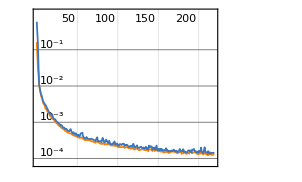
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2190  rounds:219  time:21s  examples/s:109542
data | ,,  training examples:10000  validation examples:5000  processed examples:2242560  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:1.31×10^-4
validation | ,,  loss:1.48×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.221129,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.306666,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.368496,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.384698,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.404927,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.450406,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.494775,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.459795,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.411998,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658,0.269658}

θ̂: {0.222287,0.236849,0.222897,0.224032,0.228617,0.214453,0.225847,0.215533,0.226673,0.211977,0.219467,0.220612,0.231649,0.230047,0.225416,0.239094,0.214372,0.217355,0.223542,0.233729,0.210664,0.229415,0.222063,0.232279,0.215814,0.226709,0.212341,0.22264,0.213725,0.219134,0.221246,0.217553,0.215383,0.224497,0.223697,0.215503,0.216312,0.218697,0.228042,0.218572,0.227212,0.22616,0.217822,0.225184,0.221837,0.210148,0.234859,0.225785,0.229083,0.215808,0.221063,0.219581,0.223248,0.22661,0.222843,0.230217,0.225229,0.227048,0.225538,0.217375,0.225955,0.216639,0.2202,0.228937,0.220718,0.224727,0.224447,0.22536,0.217871,0.218133,0.225643,0.209708,0.21193,0.214825,0.207739,0.213346,0.229019,0.219523,0.224145,0.232748,0.227353,0.209939,0.22706,0.216603,0.219698,0.217618,0.224089,0.219403,0.234385,0.215214,0.212115,0.223423,0.210798,0.220005,0.21259,0.213575,0.217187,0.225713,0.213913,0.220662,0.310676,0.31006,0.28681,0.322419,0.313516,0.309891,0.319806,0.295076,0.325783,0.320933,0.32554,0.31932,0.302539,0.302749,0.296345,0.286874,0.307816,0.33003,0.306064,0.298524,0.314457,0.338193,0.314186,0.291593,0.31121,0.31573,0.312039,0.307459,0.301124,0.318608,0.288444,0.327463,0.295279,0.302008,0.310682,0.325545,0.319956,0.297065,0.285185,0.275009,0.302024,0.324446,0.302581,0.333488,0.318701,0.312971,0.317152,0.283375,0.301875,0.312942,0.307925,0.307564,0.312169,0.313351,0.305768,0.284102,0.289777,0.303944,0.30549,0.296307,0.290158,0.307325,0.291135,0.318881,0.323291,0.315858,0.275193,0.32528,0.304013,0.300234,0.303881,0.308902,0.317978,0.330841,0.332235,0.287262,0.314008,0.318978,0.292725,0.290136,0.300131,0.31175,0.326952,0.312054,0.31426,0.316973,0.320036,0.299264,0.341761,0.323419,0.306987,0.303549,0.299412,0.317429,0.312663,0.310275,0.303216,0.327555,0.294981,0.315379,0.356733,0.371626,0.366313,0.348157,0.394762,0.360735,0.373528,0.357601,0.368564,0.368624,0.372256,0.355648,0.367597,0.368858,0.359575,0.370746,0.359002,0.37172,0.369377,0.379776,0.360918,0.370231,0.35678,0.361345,0.3567,0.367848,0.379692,0.351223,0.378276,0.375039,0.403048,0.352847,0.368039,0.365429,0.370086,0.383711,0.373604,0.382641,0.380657,0.37982,0.350263,0.375637,0.348552,0.372018,0.376584,0.363311,0.333602,0.376751,0.346174,0.36659,0.399791,0.372819,0.351801,0.364088,0.351715,0.362766,0.370201,0.348544,0.370294,0.353833,0.382937,0.371967,0.367797,0.369594,0.408056,0.403128,0.360012,0.368999,0.372522,0.377646,0.364459,0.372242,0.358275,0.373881,0.364204,0.369635,0.369832,0.372801,0.352064,0.355936,0.366885,0.389354,0.373399,0.391181,0.377089,0.366818,0.355931,0.361046,0.389189,0.362885,0.351542,0.375597,0.366523,0.381339,0.384609,0.385101,0.366976,0.353254,0.361684,0.336872,0.38497,0.387808,0.375522,0.386412,0.382307,0.38966,0.387664,0.384939,0.342094,0.383024,0.398216,0.370553,0.378838,0.406205,0.369584,0.387809,0.378956,0.372499,0.388083,0.401749,0.39131,0.377905,0.400924,0.372011,0.402245,0.381778,0.377694,0.406121,0.396626,0.371001,0.364555,0.389472,0.378064,0.384057,0.375895,0.393284,0.387546,0.38464,0.382577,0.387337,0.388644,0.390961,0.381856,0.368526,0.345891,0.359675,0.368806,0.365242,0.390654,0.390023,0.382213,0.390442,0.398786,0.384213,0.36584,0.394927,0.390471,0.367632,0.377121,0.362658,0.398143,0.38027,0.37433,0.395912,0.380006,0.38505,0.379519,0.411361,0.387988,0.376876,0.395618,0.375159,0.381511,0.399878,0.367314,0.3729,0.386698,0.40398,0.360428,0.409215,0.415567,0.390459,0.384938,0.366252,0.396909,0.387034,0.365188,0.374537,0.350626,0.395312,0.374646,0.40027,0.394694,0.390586,0.401113,0.384743,0.37287,0.367256,0.36092,0.392448,0.411533,0.407046,0.384622,0.374674,0.402831,0.416575,0.435959,0.414775,0.390287,0.40641,0.386144,0.401152,0.417789,0.399367,0.409454,0.408259,0.403399,0.420311,0.408309,0.382794,0.405557,0.413779,0.404237,0.389233,0.422371,0.412424,0.429645,0.402538,0.388837,0.398368,0.412269,0.422211,0.42969,0.415711,0.40179,0.4125,0.398568,0.425013,0.415055,0.391072,0.394053,0.405244,0.405897,0.388868,0.39952,0.405225,0.407044,0.399373,0.41256,0.399158,0.411145,0.40975,0.398768,0.408717,0.409456,0.409899,0.404055,0.407014,0.395537,0.408464,0.399607,0.423569,0.392978,0.420883,0.414181,0.400367,0.384369,0.409597,0.390845,0.417248,0.404949,0.412056,0.398514,0.417917,0.399287,0.404072,0.405346,0.409929,0.415011,0.408126,0.403064,0.417836,0.433717,0.416691,0.390272,0.38442,0.403141,0.400313,0.406962,0.419493,0.396115,0.421038,0.407165,0.393204,0.399437,0.369955,0.408566,0.385249,0.409191,0.410974,0.444193,0.436964,0.4587,0.442451,0.451132,0.459261,0.450319,0.45426,0.465367,0.459458,0.466815,0.457161,0.459877,0.451971,0.447879,0.458682,0.440046,0.466932,0.450661,0.472111,0.454266,0.445449,0.438108,0.435104,0.452851,0.439938,0.452541,0.455293,0.468494,0.449034,0.478588,0.440929,0.439793,0.429764,0.449633,0.444604,0.471802,0.44511,0.455767,0.444581,0.448107,0.459852,0.431868,0.475263,0.454177,0.437274,0.441809,0.461814,0.460388,0.449524,0.434819,0.440814,0.451675,0.451001,0.44308,0.460167,0.446359,0.456015,0.45762,0.454045,0.466039,0.460676,0.473058,0.447828,0.446221,0.455838,0.455568,0.459996,0.460641,0.451091,0.431677,0.449349,0.445464,0.443413,0.447646,0.465147,0.450476,0.452459,0.452998,0.458611,0.457574,0.431646,0.455679,0.448423,0.450274,0.452551,0.4417,0.445394,0.456876,0.432035,0.452781,0.422605,0.45384,0.465548,0.465582,0.448742,0.439854,0.444013,0.464258,0.451924,0.485738,0.491634,0.517733,0.480863,0.492866,0.49476,0.481408,0.487794,0.48695,0.476253,0.48179,0.492477,0.493892,0.487504,0.506722,0.500912,0.489431,0.503201,0.490254,0.487534,0.479832,0.471029,0.501617,0.483335,0.483437,0.48976,0.483941,0.478801,0.486417,0.498043,0.487978,0.487414,0.484186,0.477369,0.480549,0.487994,0.498152,0.484434,0.492831,0.486921,0.470248,0.492796,0.479393,0.484294,0.502902,0.482555,0.475574,0.492794,0.482346,0.488958,0.478906,0.492307,0.476545,0.484631,0.477062,0.472754,0.489754,0.480269,0.494218,0.490508,0.497085,0.479807,0.476525,0.479066,0.485724,0.493123,0.493358,0.494362,0.485316,0.46775,0.482077,0.491822,0.494712,0.480923,0.486394,0.496984,0.48234,0.475583,0.477444,0.503135,0.478333,0.481232,0.475423,0.479326,0.483594,0.492959,0.482633,0.480042,0.490139,0.488053,0.510788,0.488848,0.484174,0.487617,0.497197,0.485912,0.490599,0.492174,0.497758,0.500158,0.453635,0.463382,0.465694,0.464611,0.459603,0.446646,0.457393,0.453071,0.462389,0.467018,0.456318,0.459612,0.462346,0.468074,0.452081,0.467526,0.45888,0.448762,0.450254,0.46942,0.471165,0.419997,0.441519,0.458895,0.464912,0.453285,0.459626,0.46397,0.43814,0.45824,0.454173,0.450541,0.484254,0.458733,0.454335,0.459178,0.452755,0.473916,0.448164,0.446827,0.460943,0.475551,0.462665,0.459982,0.473802,0.465152,0.462921,0.455473,0.469672,0.468523,0.462749,0.443282,0.469295,0.460673,0.482215,0.46051,0.457177,0.468765,0.456984,0.453807,0.477354,0.464481,0.46146,0.456886,0.473904,0.446615,0.452806,0.457732,0.470657,0.444978,0.432343,0.450322,0.444537,0.461611,0.457349,0.455729,0.458577,0.440748,0.477093,0.444802,0.430012,0.449866,0.471689,0.450937,0.470047,0.463776,0.45585,0.442069,0.4639,0.460784,0.461842,0.426493,0.484122,0.473139,0.453695,0.455381,0.449715,0.46927,0.466222,0.482886,0.407288,0.435715,0.363821,0.398386,0.40777,0.407142,0.402794,0.398836,0.418089,0.398988,0.389305,0.412364,0.43229,0.412061,0.410979,0.419424,0.401156,0.401432,0.400024,0.403122,0.413783,0.417032,0.387311,0.404776,0.395553,0.412187,0.417671,0.422371,0.37932,0.424133,0.424702,0.426513,0.378204,0.434058,0.399493,0.394392,0.419448,0.411496,0.43767,0.429218,0.384554,0.414941,0.404444,0.400642,0.426368,0.427143,0.413887,0.4158,0.38783,0.409348,0.400481,0.430175,0.415213,0.399454,0.427344,0.442358,0.411638,0.428071,0.409529,0.426018,0.421106,0.419861,0.416739,0.408113,0.373681,0.421192,0.40883,0.388069,0.413262,0.417495,0.40742,0.392635,0.435173,0.423061,0.408716,0.439056,0.415594,0.394446,0.412404,0.426507,0.405491,0.402542,0.420953,0.414544,0.415034,0.385579,0.417955,0.405293,0.405833,0.420777,0.39947,0.431544,0.420807,0.432009,0.415423,0.414479,0.387432,0.416994,0.433122,0.435469,0.267576,0.279938,0.264881,0.265453,0.272525,0.282696,0.263507,0.283233,0.272211,0.279595,0.259523,0.265426,0.281023,0.27327,0.284742,0.282156,0.276962,0.2752,0.25813,0.281222,0.270503,0.264352,0.274772,0.265752,0.252975,0.272239,0.266417,0.276299,0.255251,0.289465,0.269741,0.272438,0.268231,0.275674,0.270828,0.272282,0.271755,0.256371,0.263709,0.267306,0.255463,0.279382,0.248023,0.268018,0.274655,0.277265,0.263503,0.249368,0.284754,0.250066,0.261165,0.269485,0.279972,0.273385,0.276123,0.269559,0.263402,0.256874,0.284502,0.259135,0.297342,0.275444,0.260381,0.268383,0.27912,0.257787,0.280513,0.262942,0.27863,0.248944,0.264253,0.276958,0.267667,0.272474,0.274865,0.258217,0.273768,0.271755,0.270352,0.258119,0.281699,0.257101,0.252247,0.261078,0.285091,0.278007,0.275027,0.268743,0.288523,0.264349,0.2593,0.235745,0.276798,0.275602,0.283268,0.280141,0.27082,0.270081,0.284531,0.261741}

abs(θ-θ̂): {0.00115798,0.0157203,0.00176799,0.00290327,0.00748866,0.0066761,0.00471837,0.00559563,0.00554403,0.00915132,0.00166144,0.000516318,0.0105205,0.00891831,0.00428728,0.0179654,0.00675651,0.00377426,0.00241328,0.0125999,0.0104653,0.00828601,0.000934638,0.0111507,0.00531494,0.00558033,0.00878812,0.00151142,0.00740398,0.00199505,0.000117354,0.00357547,0.00574555,0.00336783,0.00256833,0.00562582,0.00481711,0.00243148,0.00691353,0.00255639,0.00608311,0.00503115,0.00330649,0.00405481,0.000708527,0.010981,0.0137304,0.00465622,0.00795441,0.00532088,0.0000662137,0.00154737,0.00211904,0.00548134,0.00171395,0.00908818,0.00409994,0.00591908,0.00440902,0.00375349,0.00482663,0.00448937,0.000928604,0.0078079,0.000410922,0.00359786,0.00331859,0.00423109,0.00325792,0.00299565,0.00451385,0.0114205,0.00919833,0.00630396,0.0133895,0.00778323,0.00789031,0.00160574,0.00301637,0.0116189,0.00622382,0.0111903,0.00593094,0.0045254,0.00143061,0.00351129,0.00296012,0.00172579,0.0132557,0.00591528,0.00901388,0.00229462,0.0103306,0.0011239,0.0085387,0.00755406,0.0039421,0.00458413,0.00721563,0.000466563,0.00400999,0.00339469,0.0198552,0.0157538,0.00685077,0.00322517,0.0131407,0.0115897,0.0191172,0.0142672,0.018874,0.0126544,0.00412647,0.00391672,0.0103204,0.0197915,0.00115036,0.0233648,0.000601476,0.00814126,0.00779166,0.0315278,0.00752067,0.0150726,0.00454419,0.00906449,0.00537359,0.000793898,0.00554193,0.0119428,0.0182218,0.020797,0.0113862,0.00465757,0.00401645,0.0188793,0.0132906,0.00960053,0.0214806,0.0316564,0.00464169,0.0177805,0.00408438,0.0268221,0.0120352,0.00630536,0.0104864,0.0232903,0.0047904,0.00627648,0.00125929,0.000898743,0.00550317,0.00668549,0.000897711,0.0225639,0.0168885,0.00272164,0.00117511,0.010359,0.016508,0.00065943,0.0155307,0.0122155,0.0166258,0.00919216,0.0314726,0.0186143,0.00265244,0.00643114,0.00278462,0.002236,0.0113127,0.0241752,0.0255692,0.0194037,0.00734242,0.0123123,0.0139403,0.0165292,0.00653473,0.00508478,0.0202862,0.00538891,0.0075944,0.0103069,0.01337,0.0074015,0.0350959,0.0167536,0.000321114,0.00311682,0.00725386,0.0107639,0.00599718,0.00360983,0.00344962,0.020889,0.0116846,0.00871318,0.0117625,0.00313006,0.00218205,0.0203382,0.0262668,0.00776066,0.00503288,0.0108946,0.0000680222,0.000128223,0.00376044,0.0128478,0.000898467,0.00036232,0.00892066,0.00225095,0.00949349,0.00322412,0.000881626,0.0112803,0.00757708,0.00173585,0.011715,0.00715085,0.0117952,0.000647412,0.0111964,0.0172729,0.00978015,0.00654347,0.0345523,0.0156481,0.000456499,0.00306676,0.00159074,0.015216,0.00510873,0.014145,0.0121615,0.0113248,0.0182325,0.00714101,0.0199431,0.00352283,0.00808869,0.00518464,0.0348939,0.00825594,0.022322,0.00190534,0.0312951,0.0043235,0.0166944,0.00440799,0.0167807,0.0057291,0.001705,0.0199512,0.00179882,0.0146628,0.0144412,0.00347112,0.00069897,0.00109799,0.0395603,0.0346322,0.00848319,0.000503524,0.00402661,0.00915004,0.00403635,0.00374676,0.0102204,0.00538526,0.00429161,0.00113974,0.00133623,0.0043057,0.0164319,0.0125594,0.00161006,0.0208587,0.00490366,0.0226855,0.00859345,0.00167756,0.0125647,0.00744908,0.020693,0.00561039,0.0169532,0.00710137,0.00197299,0.0128432,0.0161134,0.0166051,0.00151901,0.0152414,0.0068119,0.0316234,0.0002718,0.00311023,0.00917574,0.00171402,0.00239074,0.00496212,0.00296557,0.000240776,0.0426044,0.00167358,0.0135177,0.0141454,0.00586,0.021507,0.0151144,0.00311092,0.00574234,0.0121994,0.00338474,0.0170514,0.00661198,0.00679341,0.0162257,0.012687,0.0175473,0.0029197,0.00700435,0.0214228,0.0119275,0.0136972,0.0201434,0.00477407,0.0066345,0.000640717,0.00880277,0.00858617,0.00284773,0.0000575749,0.00212127,0.00263927,0.00394562,0.00626281,0.00284174,0.0161717,0.0388074,0.0250229,0.0158925,0.0194557,0.0059563,0.00532511,0.002485,0.00574425,0.0140875,0.000485298,0.0188582,0.0102288,0.00577286,0.0170657,0.00757685,0.0220396,0.0134447,0.00442826,0.0103681,0.0112135,0.00469187,0.0003517,0.00517952,0.0266631,0.00328973,0.00782254,0.0109196,0.0095393,0.00318661,0.01518,0.0173837,0.0117981,0.00200022,0.0192823,0.0242696,0.0245173,0.0308687,0.00576106,0.000239852,0.0184462,0.0122105,0.00233588,0.0195097,0.0101606,0.0340716,0.010614,0.0100517,0.0155723,0.009996,0.00588766,0.0164146,0.0000449451,0.0118282,0.0174424,0.0237777,0.00774995,0.00660614,0.00211854,0.0203047,0.0302531,0.00209557,0.011648,0.0310323,0.00984792,0.0146398,0.00148265,0.0187831,0.00377514,0.0128616,0.00556036,0.00452725,0.00333191,0.00152852,0.015384,0.00338195,0.0221327,0.000630062,0.00885163,0.000689972,0.015694,0.0174436,0.00749679,0.0247184,0.00238864,0.0160902,0.00655927,0.00734184,0.0172843,0.0247634,0.0107843,0.00313662,0.00757329,0.00635861,0.0200863,0.0101275,0.0138551,0.0108745,0.000317316,0.000969779,0.016059,0.00540688,0.000298124,0.00211741,0.00555401,0.00763316,0.00576921,0.00621806,0.0048231,0.00615873,0.00379033,0.00452934,0.00497205,0.000872482,0.0020865,0.00938972,0.00353695,0.00532021,0.0186415,0.0119495,0.015956,0.00925387,0.00456019,0.0205579,0.00467024,0.0140825,0.0123212,0.000021588,0.00712941,0.00641303,0.0129902,0.00563972,0.000854928,0.000418972,0.0050023,0.0100844,0.00319869,0.00186257,0.0129085,0.0287895,0.0117644,0.014655,0.0205069,0.00178568,0.0046136,0.00203536,0.014566,0.00881191,0.0161109,0.00223763,0.0117233,0.00548982,0.034972,0.00363914,0.0196781,0.00426374,0.0060466,0.00621332,0.0134419,0.00829433,0.00795438,0.000726534,0.00885524,0.0000870396,0.00385387,0.0149614,0.0090525,0.0164093,0.00675554,0.00947086,0.00156484,0.00252642,0.00827639,0.0103602,0.0165258,0.000255628,0.0217052,0.00386022,0.00495689,0.0122976,0.015302,0.0024447,0.0104679,0.00213541,0.0048873,0.0180883,0.00137218,0.0281825,0.00947719,0.010613,0.0206419,0.00077297,0.00580196,0.0213964,0.00529631,0.00536124,0.00582455,0.00229858,0.00944663,0.0185378,0.0248573,0.00377144,0.0131319,0.00859733,0.0114078,0.0099826,0.000882344,0.0155864,0.00959189,0.00126912,0.000595523,0.0073257,0.00976158,0.00404658,0.00560905,0.00721432,0.00363929,0.0156329,0.0102705,0.0226519,0.00257747,0.00418483,0.00543175,0.00516216,0.00959004,0.0102353,0.00068499,0.0187288,0.00105675,0.00494223,0.00699251,0.00275941,0.0147415,0.0000698995,0.00205274,0.00259198,0.00820492,0.00716801,0.0187601,0.00527291,0.0019828,0.00013219,0.0021448,0.00870536,0.00501146,0.00646995,0.0183711,0.00237526,0.0278005,0.00343393,0.0151422,0.0151757,0.00166361,0.0105522,0.00639291,0.0138523,0.00151841,0.00903642,0.00314105,0.0229587,0.0139118,0.00190824,0.0000143359,0.0133671,0.00698048,0.00782478,0.0185216,0.0129845,0.00229746,0.000882805,0.00727025,0.011947,0.00613764,0.00534386,0.0084264,0.00452072,0.00724053,0.0149426,0.0237452,0.00684211,0.0114392,0.0113375,0.00501433,0.010834,0.0159738,0.00835806,0.00326827,0.00679648,0.00736091,0.0105886,0.0174057,0.0142253,0.00678089,0.00337788,0.0103403,0.00194407,0.00785324,0.024527,0.00197843,0.0153812,0.0104801,0.00812754,0.0122196,0.019201,0.00198078,0.0124289,0.00581694,0.0158687,0.00246778,0.0182295,0.0101433,0.0177125,0.0220205,0.00502104,0.0145057,0.000556261,0.00426692,0.00231039,0.0149672,0.0182501,0.0157085,0.00905025,0.00165179,0.00141648,0.000412882,0.00945851,0.0270242,0.0126977,0.00295296,0.0000626454,0.0138516,0.00838024,0.00220972,0.0124346,0.019192,0.0173309,0.00836006,0.0164416,0.0135427,0.0193515,0.0154487,0.0111804,0.00181598,0.0121411,0.0147328,0.00463528,0.00672117,0.0160131,0.00592685,0.0106007,0.00715742,0.00242233,0.00886235,0.00417596,0.00260079,0.00298378,0.0053831,0.00616023,0.00358683,0.00589892,0.0048157,0.000192224,0.0131491,0.0024026,0.00672388,0.00259328,0.00722319,0.00347686,0.000182925,0.00255081,0.00827915,0.00771433,0.00773049,0.000915526,0.0110329,0.00954106,0.00962421,0.0113694,0.0397984,0.0182761,0.000899969,0.00511715,0.00651073,0.000169306,0.00417474,0.0216553,0.00155547,0.00562253,0.00925401,0.024459,0.00106221,0.0054605,0.000616907,0.0070402,0.0141209,0.011631,0.0129683,0.00114757,0.0157562,0.00286979,0.000186236,0.0140066,0.00535685,0.00312549,0.00432256,0.00987646,0.00872767,0.00295377,0.0165138,0.00949931,0.000877888,0.0224197,0.000715108,0.00261858,0.00896979,0.00281152,0.00598848,0.0175584,0.00468594,0.00166482,0.00290897,0.0141085,0.0131806,0.0069893,0.00206289,0.0108614,0.0148177,0.0274526,0.00947365,0.0152578,0.00181559,0.00244665,0.00406635,0.00121853,0.0190475,0.0172975,0.0149937,0.0297833,0.00992951,0.0118936,0.00885859,0.0102512,0.00398085,0.00394559,0.0177259,0.00410435,0.000988932,0.00204712,0.0333019,0.024327,0.0133435,0.00610062,0.00441441,0.0100798,0.00947482,0.0064266,0.023091,0.00470998,0.0237166,0.0481774,0.0136128,0.00422856,0.00485655,0.00920426,0.0131622,0.00609059,0.0130105,0.0226933,0.00036586,0.0202914,0.0000622042,0.00101908,0.00742585,0.0108422,0.0105664,0.0119748,0.00887688,0.00178445,0.0050338,0.0246878,0.00722232,0.0164457,0.000188715,0.00567249,0.0103722,0.0326783,0.0121343,0.0127033,0.0145148,0.0337943,0.0220594,0.0125049,0.0176063,0.00744931,0.00050246,0.0256713,0.0172195,0.0274448,0.00294305,0.0075542,0.0113566,0.0143695,0.0151445,0.00188882,0.00380204,0.0241688,0.0026499,0.0115171,0.0181765,0.00321499,0.0125447,0.0153458,0.0303599,0.000360274,0.0160725,0.00246956,0.0140195,0.00910786,0.00786293,0.00474051,0.0038852,0.0383177,0.00919316,0.00316813,0.0239291,0.00126407,0.00549696,0.0045782,0.0193629,0.0231742,0.0110629,0.00328215,0.0270573,0.00359569,0.0175526,0.000405914,0.0145085,0.00650748,0.00945669,0.00895486,0.0025459,0.00303603,0.0264198,0.00595689,0.00670492,0.00616523,0.00877852,0.012528,0.0195455,0.00880904,0.0200106,0.00342477,0.00248057,0.0245669,0.00499517,0.0211234,0.0234703,0.00208214,0.0102799,0.0047777,0.00420528,0.00286624,0.0130381,0.00615081,0.0135751,0.00255269,0.00993663,0.0101353,0.00423181,0.0113643,0.00361201,0.0150839,0.0124976,0.00730378,0.00554177,0.0115278,0.0115633,0.000844422,0.00530603,0.00511357,0.00390652,0.0166835,0.00258088,0.00324115,0.00664059,0.0144068,0.0198066,0.0000831512,0.00277972,0.00142768,0.00601611,0.00116974,0.00262329,0.00209686,0.0132868,0.00594887,0.00235226,0.0141956,0.00972346,0.0216357,0.00164073,0.0049966,0.00760666,0.00615558,0.0202903,0.0150953,0.0195923,0.00849366,0.000173447,0.0103142,0.0037264,0.00646502,0.0000991794,0.00625577,0.0127847,0.0148435,0.0105233,0.0276836,0.00578574,0.00927692,0.00127518,0.00946147,0.0118709,0.0108546,0.00671586,0.00897175,0.0207139,0.00540542,0.00729978,0.00199121,0.00281611,0.00520668,0.0114417,0.00410944,0.00209675,0.000693473,0.0115393,0.0120409,0.0125571,0.0174111,0.00857982,0.0154332,0.00834844,0.00536919,0.000915048,0.0188644,0.00530961,0.0103587,0.0339134,0.00713992,0.00594408,0.0136097,0.0104827,0.00116223,0.000422689,0.0148725,0.00791728}

Difference between the true θ and the Mean for each θ: {0.000414614,0.00217761,0.0000182579,0.00154766,0.000652594,0.00116472,0.00744402,0.000983698,0.000501733,0.000317074}

Variance for each θ:{0.0000443132,0.000185619,0.000178322,0.000191249,0.00014682,0.000113864,0.0000775351,0.000138787,0.00023503,0.00011131}

crb for each θ:{0.0000371926,0.0000636756,0.0000837415,0.0000889259,0.0000952848,0.000108881,0.000120781,0.000111529,0.0000974697,0.0000518625}

ratio of variance and crb for each θ:{1.19145,2.91507,2.12944,2.15066,1.54086,1.04577,0.641946,1.2444,2.41131,2.14626}

RMSE:0.0122011

```mathematica
{Θ, e} = RunExperiment[GeometricDistribution, {0.2,0.5}];
```